```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mm=Import["Rumor Results.csv","CSV"];
steps =Dimensions[mm][[1]];
codons=Dimensions[mm][[2]]-3;
fullx=Dimensions[mm][[2]]-1;
t=Range[1,steps]; (* indexed with y on time *)
c=Range[1,codons];(* indexed with x on codons *)
f=Range[1,fullx];
```

```mathematica
ml=Import["Meme Length List.csv","CSV"];
Round[ml,0.01]//MatrixForm;

mf=Import["Rumor Fitness.csv", "CSV"];
Round[mf,0.01]//MatrixForm;
```

```mathematica
mm// MatrixForm;
mmdata=Flatten[Table[{x,y-1,mm[[y,x]]},{x,f},{y,t}],1];
mmdataf=Flatten[Table[{x,12,mf[[i,x]]},{x,c}, {i,Length[mf]}],1];
```

```mathematica
ldp=ListDensityPlot[mmdata[[1;;220]],PlotRange->{{0.5,Max[c]+0.5},{-0.5,Max[t]-1+0.5},{1,5}},InterpolationOrder->0,PlotLegends->Placed[BarLegend[{"LightTemperatureMap",{1,5}},LegendLabel->Style["MM",16,FontFamily->"Times"],LabelStyle->{Black,12,FontFamily->"Times"}],Right],ColorFunction->"LightTemperatureMap",BaseStyle->{FontFamily->"Times"},FrameLabel->{"Codon","Time Step"},LabelStyle->Directive[Black,Bold, 18],FrameTicks->{{0,Range[Max[t]-2,2],None},{Range[2,Max[c],2],None}},FrameTicksStyle->Directive[Black,12],BoundaryStyle->Directive[Gray, Thin],PlotRangeClipping->False];
```

```mathematica
ldpfid=ListDensityPlot[mmdata[[221;;231]],PlotRange->{{20.5,21.5},{-0.5,Max[t]-1+0.5},{0,100}},InterpolationOrder->0,PlotLegends->Placed[BarLegend[{Function[r,Blend[{ Darker[Green],White},r]],{0,100}},3,LegendLabel->Placed[Style["%Fidelity",16,FontFamily->"Times"],Above],LabelStyle->{Black,12,FontFamily->"Times"}],Right],ColorFunction->Function[r,Blend[{ Darker[Green],White},r]],BaseStyle->{FontFamily->"Times"},FrameLabel->{"Codon","Time Step"},LabelStyle->Directive[Black,Bold, 18],FrameTicks->{{Range[0,Max[t]-2,2],None},{Range[21,22,1],None}},FrameTicksStyle->Directive[Black,12],BoundaryStyle->Directive[Gray, Thin],PlotRangeClipping->False, ColorFunctionScaling->True];

ldpinf=ListDensityPlot[mmdata[[232;;242]],PlotRange->{{21.5,22.5},{-0.5,Max[t]-1+0.5},{0,100}},InterpolationOrder->0,PlotLegends->Placed[BarLegend[{Function[r,Blend[{ Darker[Red],White},r]],{0,100}},3,LegendLabel->Placed[Style["%Infected",16,FontFamily->"Times"],Above],LabelStyle->{Black,12,FontFamily->"Times"}],Right],ColorFunction->Function[r,Blend[{ Darker[Red],White},r]],BaseStyle->{FontFamily->"Times"},FrameLabel->{"Codon","Time Step"},LabelStyle->Directive[Black,Bold, 18],FrameTicks->{{Range[0,Max[t]-2,2],None},{Range[21,22,1],None}},FrameTicksStyle->Directive[Black,12],BoundaryStyle->Directive[Gray, Thin],PlotRangeClipping->False, ColorFunctionScaling->True];
```

```mathematica
ldpf=ListDensityPlot[mmdataf,PlotRange->{{0.5,Max[c]+0.5},{-0.5,Max[t]-1+1+0.5},{0,1}},InterpolationOrder->0,PlotLegends->Placed[BarLegend[{"PigeonTones",{0,1}},4,LegendLabel->Placed[Style["F",16,FontFamily->"Times"],Right],LabelStyle->{Black,12,FontFamily->"Times"}],Above],ColorFunction->"PigeonTones",BaseStyle->{FontFamily->"Times"},FrameLabel->{"Codon","Time Step"},LabelStyle->Directive[Black,Bold, 18],FrameTicks->{{Range[0,Max[t]-2,2],None},{Range[2,Max[c],2],None}},FrameTicksStyle->Directive[Black,12],BoundaryStyle->Directive[Gray, Thin],PlotRangeClipping->False, ColorFunctionScaling->False];
```

```mathematica
startx=0.5;
boxes=Graphics[{EdgeForm[Thick],Black,Opacity[0],
Table[Rectangle[{If[i==1,startx,startx+Total[ml[[1;;i-1,1]]]],-0.5},{If[i==1,startx+ml[[i,1]],startx+Total[ml[[1;;i,1]]]],11.5}],{i,1,Length[ml]}]
}];
```

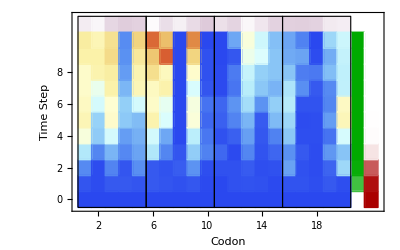

```mathematica
Show[ldpf,ldp,ldpfid,ldpinf,boxes, PlotRange->All,AspectRatio->1/1.6]
```